```mathematica
salaryAge = Import["/home/daniel/sci/name_pricing/src/salary_age.csv"];
```

```mathematica
data = salaryAge[[2;;All,1;;2]];
```

```mathematica
weights=salaryAge[[2;;All,3]];
```

```mathematica
nlm=NonlinearModelFit[data,a +b x^2+c x^3+d x^4+e x^5,{a,b,c,d,e},x,Weights->weights]
```

FittedModel[-51902.7+339.402 x^2-11.5582 x^3+0.158759 x^4-0.000816108 x^5]

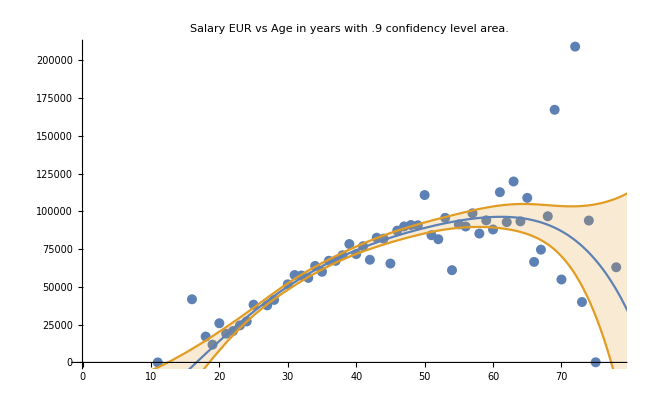

```mathematica
bands90[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.9];
plot=Show[ListPlot[data,PlotLabel->"Salary EUR vs Age in years with .9 confidency level area."],Plot[{nlm[x],bands90[x]},{x,1,100},Filling->{2->{1}}]]
```

```mathematica
Export["salary_age_09conf.png",plot];
```

salary_age_09conf.png

```mathematica
nlm//Normal
```

-51424.8+336.148 x^2-11.3976 x^3+0.155952 x^4-0.00079979 x^5

```mathematica
(*name, salary eur, count, age*)
names = Import["/home/daniel/sci/name_pricing/scraper/name_salary.csv"][[2;;All,2;;All]];
```

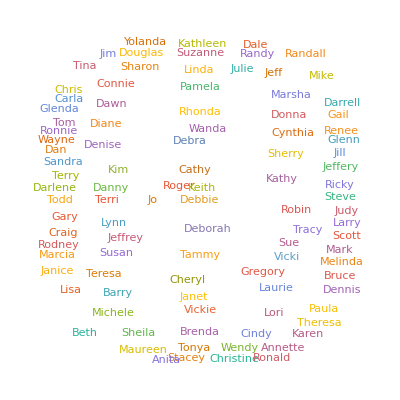

```mathematica
cloud=WordCloud[names[[All,1;;2]]]
```

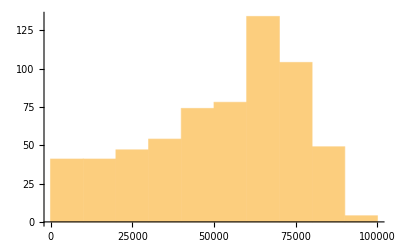

```mathematica
histogram = Histogram[names[[All,2]]]
```

```mathematica
Export["salary_cloud.png",cloud];
Export["salary_histogram.png",histogram];
```